```mathematica
Needs["ErrorBarPlots`"];
```

### Running Coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3; Nf=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; 
a4[t_]:=g4[t]^2/(4π);
```

NDSolve::precw: The precision of the differential equation ({{as'[t]==-2.25 as[t]^2-4. as[t]^3-(3863 as[t]^4)/384+1/256 as[t]^5 (-1349963/54-3564 Zeta[«1»]-9 Plus[«2»]+3 Plus[«2»]),as[10000 Log[4]]==0.0000320425},{},{},{},{}}) is less than WorkingPrecision (32.).

### Main

```mathematica
md={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}};
σmd={0.2088095376752115,0.21706712111822724,0.22532470456124298,0.23564668386501264,0.2459686631687824,0.2500974548902902,0.26496110508771864};
σmderr={0.01621039222655274,0.015928132568206136,0.015645872909859533,0.015293048336926279,0.014940223763993024,0.014799093934819724,0.014291026549795836};
βvals={6.8,6.9,7,7.125,7.25,7.3,7.48};
Tvals={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
αcont={0.5138562580709736,0.0027118637679895965};
σcont={0.16949622818854412,0.0009172672238755708};
ccont={-0.15942304870711493,0.0023023051670536016};
```

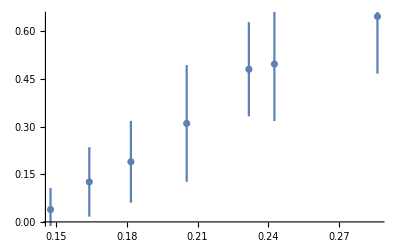

```mathematica
ErrorListPlot[Transpose[{Tvals,md[[All,1]],md[[All,2]]}]]
```

```mathematica
as[Nc_,Nf_,T_,μ_]:=(12π)/((11 Nc-2 Nf )Log[(2π √(T^2+μ^2/π^2))/0.176]);
```

```mathematica
ngam[x_]:=PolyGamma[1/2-ⅈ x]+PolyGamma[1/2+ⅈ x];
```

```mathematica
mDlo[Nc_,Nf_,T_,μ_]:=Sqrt[4 π as[Nc,Nf,T,μ](Nf(T^2/6+μ^2/(2π))+(Nc T^2)/3)];
mDBN[Nc_,Nf_,T_,μ_,c_,d_]:=Re[(4π)/3 as[Nc,Nf,T,μ] T^2(Nc+(Nc^2 as[Nc,Nf,T,μ])/(12π)(5+22 EulerGamma+22Log[(2π √(T^2+μ^2/π^2))/(4π T)])+Nf/2(1+12 μ^2/(2π T)^2)+(Nc Nf as[Nc,Nf,T,μ])/(24π)((9+132 μ^2/(2π T)^2)+22EulerGamma(1+12 μ^2/(2π T)^2)+2(7+132 μ^2/(2π T)^2)Log[(2π √(T^2+μ^2/π^2))/(4π T)]+4ngam[μ/(2π T)])+(Nf^2 as[Nc,Nf,T,μ])/(12π)(1+12 μ^2/(2π T)^2)(1-2Log[(2π √(T^2+μ^2/π^2))/(4π T)]+ngam[μ/(2π T)])-3/(8π)(Nf(Nc^2-1)as[Nc,Nf,T,μ])/Nc(1+12 μ^2/(2π T)^2)+c as[Nc,Nf,T,μ]^2+d as[Nc,Nf,T,μ]^4)];
mDcal[T_,μ_,c_,d_,Nc_,Nf_]:=(Re[Sqrt[Nc/3+Nf/6+Nf/(2 π^2)(μ/3)^2/T^2] √(4π as[Nc,Nf,T,μ])T+Nc as[Nc,Nf,T,μ] T Log[Sqrt[Nc/3+Nf/6]/as[3,3,T,0]]+c 4π as[Nc,Nf,T,μ] T+d (4π as[Nc,Nf,T,μ])^(3/2)T ])^1;
```

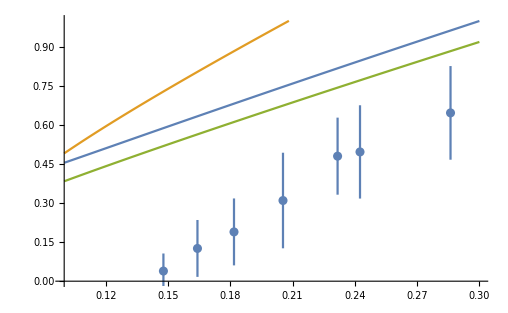

```mathematica
Show[{Plot[{mDlo[3,3,x,0.],mDcal[x,0.,0,0,3,3],Sqrt[mDBN[3,3,x,0.,0,0]]},{x,0.1,0.3},PlotRange->{0.,1.}],ErrorListPlot[Transpose[{Tvals,md[[All,1]],md[[All,2]]}]]}]
```

```mathematica
mDfit=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),(md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBN[3,3,x,0.,d,e],{d,e},x];
{k1,k2}={d,e}/.mDfit["BestFitParameters"];
mDfit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 89.3829 | 9.47282 | 9.43572 | 0.000225702
e | -118.82 | 16.6351 | -7.14274 | 0.000835302

```mathematica
mDfitu=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),((md[[n,1]]+md[[n,2]])/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBN[3,3,x,0.,d,e],{d,e},x];
{k1u,k2u}={d,e}/.mDfitu["BestFitParameters"];
mDfitu["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 151.964 | 16.9688 | 8.95549 | 0.000289414
e | -178.177 | 29.7986 | -5.97936 | 0.00187482

```mathematica
mDfitl=NonlinearModelFit[Table[{Tvals[[n]](155/172.5),((md[[n,1]]-md[[n,2]])/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2},{n,1,Length[Tvals]}],mDBN[3,3,x,0.,d,e],{d,e},x];
{k1l,k2l}={d,e}/.mDfitl["BestFitParameters"];
mDfitl["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
d | 37.0619 | 8.79057 | 4.2161 | 0.00835909
e | -57.5366 | 15.437 | -3.72719 | 0.0136105

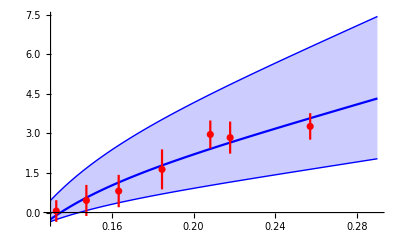

```mathematica
Show[{Plot[{mDBN[3,3,x,0.,k1,k2],mDBN[3,3,x,0.,k1u,k2u],mDBN[3,3,x,0.,k1l,k2l]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),(md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^2,(md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]))^1},{n,1,Length[Tvals]}],PlotRange->All,PlotStyle->{Red}]}]
```

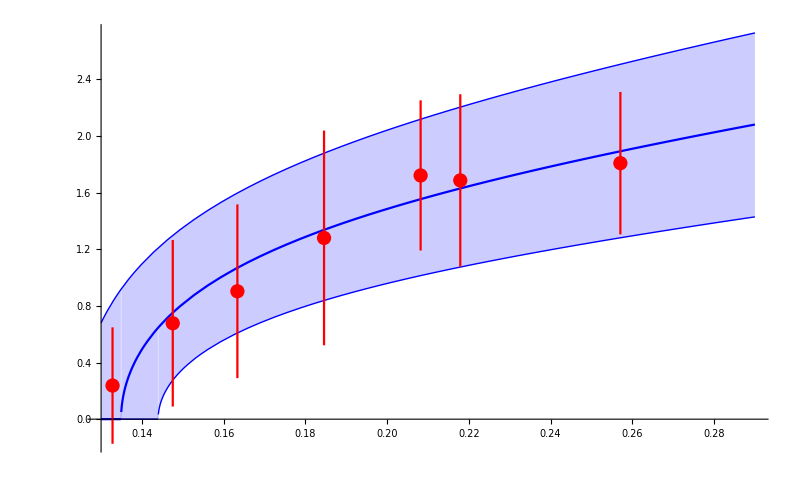

```mathematica
Show[{Plot[{Re[Sqrt[mDnlo[3,3,x,0.,k1,k2]]],Re[Sqrt[mDnlo[3,3,x,0.,k1u,k2u]]],Re[Sqrt[mDnlo[3,3,x,0.,k1l,k2l]]]},{x,0.13,0.29},PlotRange->All,Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.2,Blue],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin}}],ErrorListPlot[Table[{Tvals[[n]](155/172.5),md[[n,1]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]]),md[[n,2]]/Tvals[[n]] √(σcont[[1]]/σmd[[n]])},{n,1,Length[Tvals]}],PlotRange->All,PlotStyle->{Red}]}]
```

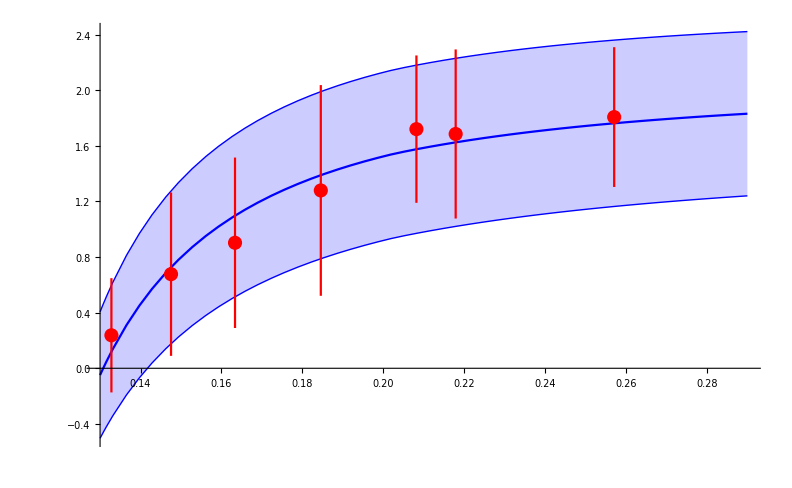

```mathematica
{Re[Sqrt[mDBN[3,3,0.155,0.,k1u,k2u]]],Re[Sqrt[mDBN[3,3,0.155,0.,k1,k2]]],Re[Sqrt[mDBN[3,3,0.155,0.,k1l,k2l]]]}
```

{1.45302,0.922262,0.470499}

```mathematica
{Re[Sqrt[mDBN[3,3,0.155,0.022,k1u,k2u]]],Re[Sqrt[mDBN[3,3,0.155,0.022,k1,k2]]],Re[Sqrt[mDBN[3,3,0.155,0.022,k1l,k2l]]]}
```

{1.45502,0.925239,0.474696}